### General wave functions

```mathematica
gam[j_,g_]:=√(j^2-g^2);
c=1/18;
qfunc1[j_,g_,ϵ_,r_,a_]:=Gamma[-a*2*gam[j,g]]/Gamma[-a*gam[j,g]-ϵ*g/(√(1-ϵ^2))](2 √(1-ϵ^2)*r)^(a*gam[j,g])Hypergeometric1F1[a*gam[j,g]-(ϵ*g)/(√(1-ϵ^2)),1+a*2*gam[j,g],2 √(1-ϵ^2)r];
qfunc2[j_,g_,ϵ_,r_,a_]:=Gamma[-a*2*gam[j,g]]/Gamma[-a*gam[j,g]-ϵ*g/(√(1-ϵ^2))]*(a*gam[j,g]-(ϵ*g)/(√(1-ϵ^2)))/(j+g/√(1-ϵ^2))(2 √(1-ϵ^2)*r)^(a*gam[j,g])Hypergeometric1F1[1+a*gam[j,g]-(ϵ*g)/(√(1-ϵ^2)),1+a*2*gam[j,g],2*√(1-ϵ^2)*r];
```

```mathematica
OutsF[j_,g_,ϵ_,r_]:=Exp[-2 √(1-ϵ^2)*r/2]*√(1+ϵ)*(2 √(1-ϵ^2)*r)^(-1/2)(qfunc1[j,g,ϵ,r,1]+qfunc1[j,g,ϵ,r,-1]+qfunc2[j,g,ϵ,r,1]+qfunc2[j,g,ϵ,r,-1]);
OutsG[j_,g_,ϵ_,r_]:=Exp[-2 √(1-ϵ^2)*r/2]*√(1-ϵ)*(2 √(1-ϵ^2)*r)^(-1/2)(qfunc1[j,g,ϵ,r,1]+qfunc1[j,g,ϵ,r,-1]-qfunc2[j,g,ϵ,r,1]-qfunc2[j,g,ϵ,r,-1]);
```

```mathematica
(*For g=0.916*)
```

```mathematica
(*Normalization*)
re916=NIntegrate[r*(OutsF[1/2,0.916,-0.99,r]^2+OutsG[1/2,0.916,-0.99,r]^2),{r,1/18,20}]
re10=NIntegrate[r*(OutsF[1/2,1.0,0.53,r]^2+OutsG[1/2,1.0,0.53,r]^2),{r,1/18,20}];
```

2.28148×10^-7+0. ⅈ

```mathematica
re8=NIntegrate[r*(OutsF[1/2,0.8,-0.48,r]^2+OutsG[1/2,0.8,-0.48,r]^2),{r,1/18,20}]
```

0.227006+0. ⅈ

```mathematica
re9=NIntegrate[r*(OutsF[1/2,0.9,-0.92,r]^2+OutsG[1/2,0.9,-0.92,r]^2),{r,1/18,20}];
```

```mathematica
re7=NIntegrate[r*(OutsF[1/2,0.7,-0.098,r]^2+OutsG[1/2,0.7,-0.098,r]^2),{r,1/18,20}]
```

0.28047+0. ⅈ

```mathematica
re6=NIntegrate[r*(OutsF[1/2,0.6,0.2198,r]^2+OutsG[1/2,0.6,0.2198,r]^2),{r,1/18,20}]
```

0.365794+0. ⅈ

```mathematica
re5=NIntegrate[r*(OutsF[1/2,0.501,0.4715,r]^2+OutsG[1/2,0.501,0.4715,r]^2),{r,1/18,20}]
```

0.513642+0. ⅈ

```mathematica
re55=NIntegrate[r*(OutsF[1/2,0.55,0.3553,r]^2+OutsG[1/2,0.55,0.3553,r]^2),{r,1/18,20}]
```

0.430143+0. ⅈ

```mathematica
re65=NIntegrate[r*(OutsF[1/2,0.65,0.0693,r]^2+OutsG[1/2,0.65,0.0693,r]^2),{r,1/18,20}]
```

0.317367+0. ⅈ

```mathematica
re75=NIntegrate[r*(OutsF[1/2,0.75,-0.280993,r]^2+OutsG[1/2,0.75,-0.280993,r]^2),{r,1/18,20}]
```

0.251801+0. ⅈ

```mathematica
re85=NIntegrate[r*(OutsF[1/2,0.85,-0.693607,r]^2+OutsG[1/2,0.85,-0.693607,r]^2),{r,1/18,20}]
```

0.191743+0. ⅈ

```mathematica
u[j_,g_,ϵ_]:=NIntegrate[(OutsF[j,g,ϵ,x]^2+OutsG[j,g,ϵ,x]^2)(OutsF[j,g,ϵ,y]^2+OutsG[j,g,ϵ,y]^2)*x*y*1/(√(x^2+y^2-2*x*y*Cos[ϕ])),{x,1/18,20},{y,1/18,20},{ϕ,0,2π}];
```

```mathematica
u[1/2,0.55,0.3553]*1/(2π*Re[re55]^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.71323  + 0.\ ⅈ and 0.00274635 for the integral and error estimates.

1.4737+0. ⅈ

```mathematica
u[1/2,0.6,0.2198]*1/(2π*Re[0.36579]^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38414  + 0.\ ⅈ and 0.00229587 for the integral and error estimates.

1.6464+0. ⅈ

```mathematica
u[1/2,0.65,0.0693]*1/(2π*Re[re65]^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.15387  + 0.\ ⅈ and 0.00192177 for the integral and error estimates.

1.82329+0. ⅈ

```mathematica
u[1/2,0.75,-0.280993]*1/(2π*Re[re75]^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.870444  + 0.\ ⅈ and 0.00141103 for the integral and error estimates.

2.18497+0. ⅈ

```mathematica
u[1/2,0.85,-0.693607]*1/(2π*Re[re85]^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.581335  + 0.\ ⅈ and 0.000990209 for the integral and error estimates.

2.51657+0. ⅈ

```mathematica
(*For g=0.8*)
```

```mathematica
NIntegrate[r*(OutsF[1/2,0.8,-0.476,r]*Conjugate[OutsF[1/2,0.8,-0.476,r]]+OutsG[1/2,0.8,-0.476,r]*Conjugate[OutsG[1/2,0.8,-0.476,r]]),{r,1/18,90},Method->"AdaptiveMonteCarlo"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in r near {r} = {0.998124}. NIntegrate obtained 2.9221×10^38 + 0.\ ⅈ and 7.20806×10^36 for the integral and error estimates.

2.9221×10^38+0. ⅈ

```mathematica
out1[ϵ_,r_,p_,n_,j_,g_]:=Exp[-2 √(1-ϵ^2)*r/2]*(2 √(1-ϵ^2)*r)^(-1/2)√(1+p)((j+g/√(1-p^2))Hypergeometric1F1[-n,1+2 √(j^2-g^2),2 √(1-p^2)*r]-n*Hypergeometric1F1[1-n,1+2 √(j^2-g^2),2 √(1-p^2)*r]);
out2[r_,p_,n_,j_,g_]:=Exp[-2 √(1-ϵ^2)*r/2]*(2 √(1-ϵ^2)*r)^(-1/2)√(1-p)((j+g/√(1-p^2))Hypergeometric1F1[-n,1+2 √(j^2-g^2),2 √(1-p^2)*r]+n*Hypergeometric1F1[1-n,1+2 √(j^2-g^2),2 √(1-p^2)*r]);
```

```mathematica
out1[-0.8,1,-0.8,1,1/2,0.916]
```

0.0676731+0.249212 ⅈ

```mathematica
Hypergeometric1F1[1-1000000000*I,1+0.5*I,0.0001]
```

-1.13448×10^192+9.46203×10^191 ⅈ

```mathematica
qfunc1[1/2,0.916,-0.99,200,1]-qfunc1[1/2,0.916,-0.99,200,-1]
```

0.+2.93623×10^28 ⅈ

```mathematica
epluseminus[ϵ_,g_]:=√(ϵ^2+(g/(1/18))^2+2*ϵ*g/(1/18)-1);
pbi[ϵ_,g_,x_,j_]:=1/2 √(-1+324 g^2+36 g ϵ+ϵ^2) (BesselJ[-3/2+j,x √(-1+324 g^2+36 g ϵ+ϵ^2)]-BesselJ[1/2+j,x √(-1+324 g^2+36 g ϵ+ϵ^2)]);
Ai[ϵ_,g_,r_,j_]:=√r BesselJ[j-1/2,epluseminus[ϵ,g]*r];
Bi[ϵ_,g_,r_,j_]:=-1/(1+ϵ+g/(1/18))((1/2-j)/(√r)BesselJ[j-1/2,epluseminus[ϵ,g]*r]+√r*pbi[ϵ,g,r,j]);
```

```mathematica
Insideratio[ϵ_,g_,r_,j_]:=Ai[ϵ,g,r,j]/Bi[ϵ,g,r,j];
```

```mathematica
FindRoot[OutsF[1/2,0.55,ϵ,1/18]/OutsG[1/2,0.55,ϵ,1/18]-Insideratio[ϵ,0.55,1/18,1/2],{ϵ,0.1}]
```

{ϵ→0.914468+0. ⅈ}

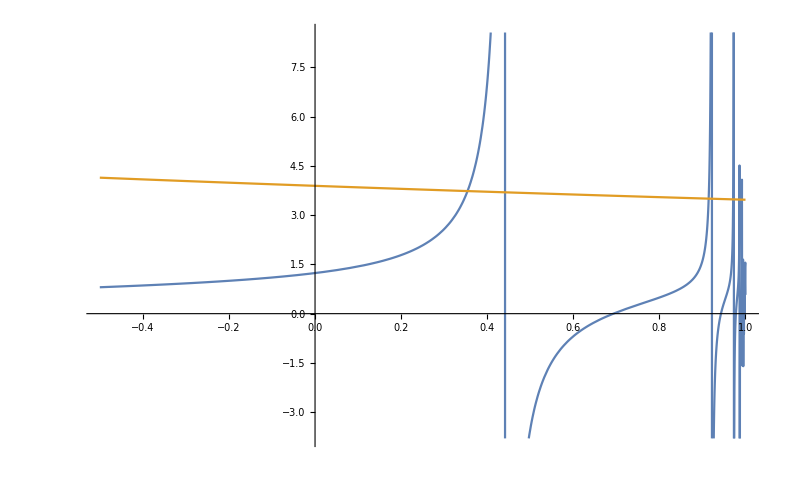

```mathematica
Plot[{Re[OutsF[1/2,0.55,ϵ,1/18]/OutsG[1/2,0.55,ϵ,1/18]],Insideratio[ϵ,0.55,1/18,1/2]},{ϵ,-0.5,1}]
```

```mathematica
e1={{0.1,0.9803},{0.2,0.9208},{0.3,0.8196},{0.4,0.6719},{0.501,0.4715},{0.6,0.2198},{0.65,0.0693},{0.7,-0.098},{0.725,-0.187644},{0.75,-0.280993},{0.775,-0.37833},{0.8,-0.48},{0.825,-0.584737},{0.85,-0.693607},{0.875,-0.806041},{0.9,-0.92},{0.916,-1}};
```

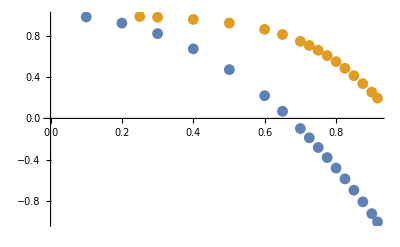

```mathematica
ListPlot[{e1,e2}]
```

```mathematica
e2={{0.25,0.9852},{0.3,0.9779},{0.4,0.9565},{0.501,0.9217},{0.6,0.8604},{0.65,0.810912},{0.7,0.745219},{0.725,0.704784},{0.75,0.658739},{0.775,0.606764},{0.8,0.54862},{0.825,0.484153},{0.85,0.413283},{0.875,0.336002},{0.9,0.2537},{0.916,0.1961}};
```

```mathematica
Export["e1.dat",e1]
```

e1.dat

```mathematica
Export["e2.dat",e2]
```

e2.dat

### J term (g=0.8) (defintions here in this subsection)

```mathematica
Jgeneral[j_,g_,ϵ_,sd_]:=NIntegrate[(x*y)/(√(x^2+y^2-2*x*y*(Cos[θ]Cos[ϕ]+Sin[θ]Sin[ϕ])))*(OutsF[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsF[j,g,ϵ,x]]+OutsG[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsG[j,g,ϵ,x]]*phase1[sd,x,θ])*(OutsF[j,g,ϵ,Dist[sd,y,ϕ]]*Conjugate[OutsF[j,g,ϵ,y]]+OutsG[j,g,ϵ,Dist[sd,y,ϕ]]*Conjugate[OutsG[j,g,ϵ,y]]*phase2[sd,y,ϕ]),{x,1/18,20},{y,1/18,20},{θ,0,2π},{ϕ,0,2π},Method->"AdaptiveMonteCarlo"];
```

```mathematica
Jgeneral[1/2,1.0,0.53,1.5]
```

1.63948+0.000508907 ⅈ

```mathematica
Jgeneraldot8=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
Jgeneraldot8[[i]]=Re[Jgeneral[1/2,0.8,-0.48,0.6+0.05*(i-1)]]
];
Export["Jgeneral8.dat",Jgeneraldot8]
```

$Aborted

Jgeneral8.dat

```mathematica
Jgeneraldot8[[1]]=Re[Jgeneral[1/2,0.8,-0.48,0.6]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.943729  - 2.20722×10^-10\ ⅈ and 0.996911 for the integral and error estimates.

0.943729

```mathematica
Jgeneraldot8[[3]]=Re[Jgeneral[1/2,0.8,-0.48,0.6+0.05*(3-1)]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.666421  - 0.0000345539\ ⅈ and 0.864237 for the integral and error estimates.

0.666421

```mathematica
Export["Jgeneral8.dat",Jgeneraldot8]
```

Jgeneral8.dat

```mathematica
Jgeneraldot8
```

{0.943729,0.711505,0.666421,0.631462,0.560623,0.420384,0.336446,0.299153,0.234693,0.212677,0.184148,0.162634,0.148516,0.12478,0.0948337,0.092776,0.0752263,0.0723092,0.0600728,0.043187,0.0481389,0.0406241,0.0348758,0.030566,0.0282397,0.024312,0.0220238,0.0185638,0.0162984,0.0146552,0.0116572,0.0119014,0.0104109,0.00907316,0.00781305,0.00746291,0.00647988,0.00564538,0.00449715,0.00436295,0.0039254,0.00341851,0.00312899,0.0027237,0.00246995,0.0021136,0.00198007,0.00175649,0.0014787,0.00111775,0.00126575,0.00113453,0.000987516,0.000881699,0.000754505,0.000721111,0.000656759,0.000579948,0.000527938,0.000465036}

### J (g=0.6)

```mathematica
Jgeneraldot6=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
Jgeneraldot6[[i]]=Re[Jgeneral[1/2,0.6,0.2198,0.6+0.05*(i-1)]]
];
```

```mathematica
Export["Jgeneral6.dat",Jgeneraldot6]
```

Jgeneral6.dat

```mathematica
J6=Table[Null,{i,60}];
```

```mathematica
For[i=1,i<61,i++,J6[[i]]={(i-1)*0.05+0.60,Jgeneraldot6[[i]]*N[1/(2*re6^2*(2π)^2)]}]
```

```mathematica
Export["J6.dat",J6]
```

J6.dat

### t_ij (g=0.8)

```mathematica
tgeneral[j_,g_,ϵ_,sd_]:=NIntegrate[x*(OutsF[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsF[j,g,ϵ,x]]+OutsG[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsG[j,g,ϵ,x]]*phase1[sd,x,θ])*(1/(√(x^2+sd^2-2*x*sd*Cos[θ]))+1/(√(x^2+sd^2-2*x*sd*Cos[π/2-θ]))+1/(√(x^2+sd^2-2*x*sd*Cos[π/2+θ]))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]-sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]+sd)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]-sd)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]+sd)^2))),{x,1/18,20},{θ,0,2π},Method->"AdaptiveMonteCarlo"];
```

```mathematica
tgeneral[1/2,0.9,-0.92,1.5]
```

7.53434×10^-7-1.02501×10^-8 ⅈ

```mathematica
tgeneraldot8=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot8[[i]]=Re[tgeneral[1/2,0.8,-0.48,0.6+0.05*(i-1)]]
];
Export["tgeneraldot8.dat",tgeneraldot8]
```

tgeneraldot8.dat

```mathematica
tgeneraldot8
```

{8.86064,7.38388,6.73123,6.00361,5.30885,4.6505,4.23793,3.77967,3.32997,3.0414,2.71627,2.4519,2.20267,1.97252,1.79792,1.61257,1.45465,1.29419,1.21773,1.08445,0.992362,0.903329,0.826813,0.76271,0.7025,0.629037,0.597315,0.528571,0.495849,0.445252,0.413824,0.384145,0.350862,0.318588,0.296536,0.270384,0.244328,0.229119,0.212332,0.202187,0.177429,0.164241,0.150291,0.139374,0.129552}

```mathematica
tgeneral8sqext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral8sqext[[i]]=Re[tgeneral[1/2,0.8,-0.48,3.6+0.05*(i-1)]]
];
Export["tgeneral8sqext.dat",tgeneral8sqext]
```

tgeneral8sqext.dat

### J (g=0.9)

```mathematica
Jgeneraldot9=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
Jgeneraldot9[[i]]=Re[Jgeneral[1/2,0.9,-0.92,0.6+0.05*(i-1)]]
];
Export["Jgeneral9normal.dat",Jgeneraldot9]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0283943  - 4.61978×10^-7\ ⅈ and 0.0540002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0254612  - 6.52412×10^-7\ ⅈ and 0.0457155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0217397  + 2.62739×10^-7\ ⅈ and 0.0389551 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 36 recursive bisections in x near {x, y, θ, ϕ} = {1.1191261678554833588430119665810340694425026914003855032975947188, 1.2425353490625792817233580615074444697481212871012649479337085967, 6.021393138320800308971314507289207540452480316162109375, 6.021393138320800308971314507289207540452480316162109375}. NIntegrate obtained 0.00209399  + 9.14901×10^-7\ ⅈ and 0.00488088 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 36 recursive bisections in x near {x, y, θ, ϕ} = {1.1191261678554833588430119665810340694425026914003855032975947188, 1.2425353490625792817233580615074444697481212871012649479337085967, 6.021393138320800308971314507289207540452480316162109375, 6.021393138320800308971314507289207540452480316162109375}. NIntegrate obtained 0.00201802  + 8.49167×10^-7\ ⅈ and 0.00374161 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 36 recursive bisections in ϕ near {x, y, θ, ϕ} = {1.1852878556586218761729342994618795566165868567282754778973207227, 1.1852878556586218761729342994618795566165868567282754778973207227, 6.021393138320800308971314507289207540452480316162109375, 6.18907456524354149252076240372844040393829345703125}. NIntegrate obtained 0.000337489  - 1.48483×10^-6\ ⅈ and 0.00250179 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

Jgeneral9normal.dat

```mathematica
Jgeneraldot9[[2]]=Re[Jgeneral[1/2,0.9,-0.92,0.6+0.05]]
```

0.023569

Jgeneral9.dat

### J (g=0.7)

```mathematica
Jgeneraldot7=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
Jgeneraldot7[[i]]=Re[Jgeneral[1/2,0.7,-0.098,0.6+0.05*(i-1)]]
];
Export["Jgeneral7.dat",Jgeneraldot7]
```

$Aborted

Jgeneral7.dat

```mathematica
Jgeneral7=Flatten[Import["Jgeneral7.dat"]]
```

{1.71531,1.45917,1.42326,1.17344,1.12177,0.965237,0.815339,0.753253,0.669329,0.563986,0.487493,0.388866,0.389511,0.338246,0.316888,0.273023,0.26416,0.219012,0.137568,0.143852,0.12961,0.134116,0.111977,0.102376,0.0921245,0.081894,0.0732343,0.0608414,0.0563929,0.04834,0.0450329,0.0249237,0.0321335,0.032486,0.0285853,0.0257623,0.0226062,0.0200426,0.0183657,0.0154509,0.0129159,0.0123513,0.0117328,0.00833075,0.00846348,0.00799242,0.00648862,0.00620014,0.00562218,0.00484187,0.00428573,0.0039847,0.0035783,0.00318362,0.00243746,0.00251771,0.00220906,0.00200991,0.00178707,0.00163121}

```mathematica
Jgeneral7[[20]]=Re[Jgeneral[1/2,0.7,-0.098,0.6+0.05*(20-1)]]
```

0.175721

```mathematica
Jgeneral7
```

{1.71531,1.45917,1.42326,1.17344,1.12177,0.965237,0.815339,0.753253,0.669329,0.563986,0.487493,0.388866,0.389511,0.338246,0.316888,0.273023,0.26416,0.219012,0.189547,0.175721,0.146039,0.134116,0.111977,0.102376,0.0921245,0.081894,0.0732343,0.0608414,0.0563929,0.04834,0.0450329,0.0408786,0.0321335,0.032486,0.0285853,0.0257623,0.0226062,0.0200426,0.0183657,0.0154509,0.0129159,0.0123513,0.0117328,0.00833075,0.00846348,0.00799242,0.00648862,0.00620014,0.00562218,0.00484187,0.00428573,0.0039847,0.0035783,0.00318362,0.00243746,0.00251771,0.00220906,0.00200991,0.00178707,0.00163121}

```mathematica
Export["Jgeneral7.dat",Jgeneral7]
```

Jgeneral7.dat

```mathematica
Jgeneral[1/2,0.7,-0.098,3.3]
```

0.00283475+7.3394×10^-6 ⅈ

### t(g=0.916) square lattice

```mathematica
tgeneraldot916sq=Table[Null,{i,60}];
For[
i=1,
i<61,
i++,
tgeneraldot916sq[[i]]=Re[tgeneral[1/2,0.916,-0.99,0.6+0.05*(i-1)]]
];
Export["tgeneraldot916sq.dat",tgeneraldot916sq]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.127579, 0.999984}. NIntegrate obtained 8.91131×10^-8 + 5.8785×10^-10\ ⅈ and 1.05516×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.130089, 0.99999}. NIntegrate obtained 7.97885×10^-8 - 6.25959×10^-10\ ⅈ and 8.40497×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.132592, 4.8079×10^-7}. NIntegrate obtained 7.38126×10^-8 + 9.80395×10^-11\ ⅈ and 1.20799×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
tgeneral916sqext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral916sqext[[i]]=Re[tgeneral[1/2,0.916,-0.99,3.6+0.05*(i-1)]]
];
Export["tgeneral916sqext.dat",tgeneral916sqext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.177765, 9.95221×10^-9}. NIntegrate obtained 1.29334×10^-8 + 9.40626×10^-11\ ⅈ and 2.48343×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.180223, 0.999996}. NIntegrate obtained 1.11514×10^-8 - 3.25958×10^-10\ ⅈ and 2.86847×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.182724, 0.999998}. NIntegrate obtained 1.02754×10^-8 - 2.32747×10^-10\ ⅈ and 2.04969×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral916sqext.dat

```mathematica
tgeneral916sqext
```

{1.29334×10^-8,1.11514×10^-8,1.02754×10^-8,9.17742×10^-9,8.38612×10^-9,7.1348×10^-9,6.15221×10^-9,5.40281×10^-9,4.74346×10^-9,4.26855×10^-9,3.9392×10^-9,3.02972×10^-9,2.68553×10^-9,2.03402×10^-9,2.00603×10^-9,1.14471×10^-9,7.64573×10^-10,5.60511×10^-10,3.01474×10^-10,-3.30462×10^-11,-2.26156×10^-10,-3.51734×10^-10,-4.72345×10^-10,-7.9438×10^-10,-1.28363×10^-9,-7.39783×10^-10,-1.07647×10^-9,-1.22562×10^-9,-1.51611×10^-9}

### t(g=0.6) square lattice

```mathematica
tgeneraldot6sq=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot6sq[[i]]=Re[tgeneral[1/2,0.6,0.2198,0.6+0.05*(i-1)]]
];
Export["tgeneraldot6sq.dat",tgeneraldot6sq]
```

tgeneraldot6sq.dat

```mathematica
tgeneral6sqext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral6sqext[[i]]=Re[tgeneral[1/2,0.6,0.2198,3.6+0.05*(i-1)]]
];
Export["tgeneral6sqext.dat",tgeneral6sqext]
```

tgeneral6sqext.dat

### t(g=0.9) sqare lattice

```mathematica
tgeneraldot9sq=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot9sq[[i]]=Re[tgeneral[1/2,0.9,-0.92,0.6+0.05*(i-1)]]
];
Export["tgeneraldot9sq.dat",tgeneraldot9sq]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.0874746, 0.999989}. NIntegrate obtained 0.0876508  - 0.000482518\ ⅈ and 0.00106399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.137598, 0.999992}. NIntegrate obtained 0.0135485  + 0.000140314\ ⅈ and 0.000170462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.14763, 0.0000155836}. NIntegrate obtained 0.00944645  - 0.00010264\ ⅈ and 0.000110957 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneraldot9sq.dat

```mathematica
tgeneral9sqext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral9sqext[[i]]=Re[tgeneral[1/2,0.9,-0.92,3.6+0.05*(i-1)]]
];
Export["tgeneral9sqext.dat",tgeneral9sqext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.177714, 2.26655×10^-6}. NIntegrate obtained 0.00286926  + 0.0000684077\ ⅈ and 0.0000415874 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.180222, 5.05918×10^-6}. NIntegrate obtained 0.00264259  - 0.0000160128\ ⅈ and 0.0000485277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.18273, 3.17148×10^-6}. NIntegrate obtained 0.00242692  - 0.0000521884\ ⅈ and 0.0000496817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral9sqext.dat

### t(g=0.7) square lattice

```mathematica
tgeneraldot7sq=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot7sq[[i]]=Re[tgeneral[1/2,0.7,-0.098,0.6+0.05*(i-1)]]
];
Export["tgeneraldot7sq.dat",tgeneraldot7sq]
```

tgeneraldot7sq.dat

```mathematica
tgeneral7sqext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral7sqext[[i]]=Re[tgeneral[1/2,0.7,-0.098,3.6+0.05*(i-1)]]
];
Export["tgeneral7sqext.dat",tgeneral7sqext]
```

tgeneral7sqext.dat

### t(g=0.916) triangular

```mathematica
tgeneraltri[j_,g_,ϵ_,sd_]:=NIntegrate[x*(OutsF[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsF[j,g,ϵ,x]]+OutsG[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsG[j,g,ϵ,x]]*phase1[sd,x,θ])*(1/(√(x^2+sd^2-2*x*sd*Cos[θ]))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-3*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-3*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-3*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]+3*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]+3*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]-5*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-5*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ]+√3*sd)^2))),{x,1/18,20},{θ,0,2π}];
```

```mathematica
tgeneraltri[1/2,0.916,-0.99,2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x, θ} = {2.00005, 0.000120264}. NIntegrate obtained 5.70212×10^-7 - 8.92546×10^-21\ ⅈ and 6.16717×10^-10 for the integral and error estimates.

5.70212×10^-7-8.92546×10^-21 ⅈ

```mathematica
tgeneraldot916tri=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot916tri[[i]]=Re[tgeneraltri[1/2,0.916,-0.99,0.6+0.05*(i-1)]]
];
Export["tgeneraldot916tri.dat",tgeneraldot916tri]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.142614, 0.0000100524}. NIntegrate obtained 9.86532×10^-8 - 1.41557×10^-9\ ⅈ and 1.02105×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.160185, 0.999994}. NIntegrate obtained 4.73124×10^-8 + 1.037×10^-9\ ⅈ and 9.63302×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.165175, 0.999996}. NIntegrate obtained 4.05677×10^-8 - 3.67292×10^-10\ ⅈ and 8.92605×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneraldot916tri.dat

```mathematica
tgeneral916triext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral916triext[[i]]=Re[tgeneraltri[1/2,0.916,-0.99,3.6+0.05*(i-1)]]
];
Export["tgeneral916triext.dat",tgeneral916triext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.177715, 0.999991}. NIntegrate obtained 2.16517×10^-8 - 1.43279×10^-10\ ⅈ and 2.9398×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.180199, 3.53511×10^-6}. NIntegrate obtained 1.90652×10^-8 + 2.33527×10^-10\ ⅈ and 6.52327×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.182741, 1.50427×10^-8}. NIntegrate obtained 1.7069×10^-8 - 2.42492×10^-10\ ⅈ and 3.06413×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral916triext.dat

### t(g=0.6) triangular

```mathematica
tgeneraldot6tri=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot6tri[[i]]=Re[tgeneraltri[1/2,0.6,0.2198,0.6+0.05*(i-1)]]
];
Export["tgeneraldot6tri.dat",tgeneraldot6tri]
```

tgeneraldot6tri.dat

```mathematica
tgeneral6triext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral6triext[[i]]=Re[tgeneraltri[1/2,0.6,0.2198,3.6+0.05*(i-1)]]
];
Export["tgeneral6triext.dat",tgeneral6triext]
```

tgeneral6triext.dat

### t(g=0.9) triangular

```mathematica
tgeneraldot9tri=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot9tri[[i]]=Re[tgeneraltri[1/2,0.9,-0.92,0.6+0.05*(i-1)]]
];
Export["tgeneraldot9tri.dat",tgeneraldot9tri]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.147638, 7.90779×10^-6}. NIntegrate obtained 0.0172499  - 0.000100888\ ⅈ and 0.000174017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.167679, 5.44895×10^-6}. NIntegrate obtained 0.00728278  + 0.000180272\ ⅈ and 0.0000898335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.1727, 0.999997}. NIntegrate obtained 0.00589895  - 2.21079×10^-6\ ⅈ and 0.0000746638 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneraldot9tri.dat

```mathematica
tgeneral9triext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral9triext[[i]]=Re[tgeneraltri[1/2,0.9,-0.92,3.6+0.05*(i-1)]]
];
Export["tgeneral9triext.dat",tgeneral9triext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.17771, 5.29712×10^-8}. NIntegrate obtained 0.004562  + 0.000155567\ ⅈ and 0.0000566853 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.180228, 0.999997}. NIntegrate obtained 0.00406643  + 0.0000919835\ ⅈ and 0.0000815826 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.182722, 0.999996}. NIntegrate obtained 0.00355589  + 0.00001638\ ⅈ and 0.0000667398 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral9triext.dat

### t(g=0.8) triangular

```mathematica
tgeneraldot8tri=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot8tri[[i]]=Re[tgeneraltri[1/2,0.8,-0.48,0.6+0.05*(i-1)]]
];
Export["tgeneraldot8tri.dat",tgeneraldot8tri]
```

tgeneraldot8tri.dat

```mathematica
tgeneral8triext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral8triext[[i]]=Re[tgeneraltri[1/2,0.8,-0.48,3.6+0.05*(i-1)]]
];
Export["tgeneral8triext.dat",tgeneral8triext]
```

tgeneral8triext.dat

### t(g=0.7) triangular

```mathematica
tgeneraldot7tri=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot7tri[[i]]=Re[tgeneraltri[1/2,0.7,-0.098,0.6+0.05*(i-1)]]
];
Export["tgeneraldot7tri.dat",tgeneraldot7tri]
```

tgeneraldot7tri.dat

```mathematica
tgeneral7triext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral7triext[[i]]=Re[tgeneraltri[1/2,0.7,-0.098,3.6+0.05*(i-1)]]
];
Export["tgeneral7triext.dat",tgeneral7triext]
```

tgeneral7triext.dat

### t(g=0.916) honeycomb

```mathematica
tgeneralhc[j_,g_,ϵ_,sd_]:=NIntegrate[x*(OutsF[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsF[j,g,ϵ,x]]+OutsG[j,g,ϵ,Dist[sd,x,θ]]*Conjugate[OutsG[j,g,ϵ,x]]*phase1[sd,x,θ])*(1/(√(x^2+sd^2-2*x*sd*Cos[θ]))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-sd-sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-sd-sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]-2*sd-sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-2*sd-sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]+2*sd)^2+(x*Sin[θ])^2))),{x,1/18,20},{θ,0,2π},Method->"AdaptiveMonteCarlo"];
```

```mathematica
tgeneralhc[1/2,0.916,-0.99,1.5]
```

1.17683×10^-6-1.57443×10^-9 ⅈ

```mathematica
tgeneraldot916hc=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot916hc[[i]]=Re[tgeneralhc[1/2,0.916,-0.99,0.6+0.05*(i-1)]]
];
Export["tgeneraldot916hc.dat",tgeneraldot916hc]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.137605, 0.999949}. NIntegrate obtained 9.01107×10^-8 + 1.77632×10^-9\ ⅈ and 1.1489×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.147636, 0.999991}. NIntegrate obtained 6.13522×10^-8 + 1.10767×10^-9\ ⅈ and 1.02715×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.152629, 0.999997}. NIntegrate obtained 4.96931×10^-8 + 7.23289×10^-10\ ⅈ and 5.48785×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneraldot916hc.dat

```mathematica
tgeneral916hcext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral916hcext[[i]]=Re[tgeneral[1/2,0.916,-0.99,3.6+0.05*(i-1)]]
];
Export["tgeneral916hcext.dat",tgeneral916hcext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.177728, 1.48×10^-6}. NIntegrate obtained 1.23727×10^-8 + 3.48782×10^-10\ ⅈ and 3.6339×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.18022, 6.33662×10^-6}. NIntegrate obtained 1.2228×10^-8 + 6.9342×10^-10\ ⅈ and 4.85496×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.18273, 0.999999}. NIntegrate obtained 1.07026×10^-8 + 4.6484×10^-11\ ⅈ and 1.52392×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral916hcext.dat

### t(g=0.6) honeycomb

```mathematica
tgeneraldot6hc=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot6hc[[i]]=Re[tgeneralhc[1/2,0.6,0.2198,0.6+0.05*(i-1)]]
];
Export["tgeneraldot6hc.dat",tgeneraldot6hc]
```

tgeneraldot6hc.dat

```mathematica
tgeneral6hcext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral6hcext[[i]]=Re[tgeneralhc[1/2,0.6,0.2198,3.6+0.05*(i-1)]]
];
Export["tgeneral6hcext.dat",tgeneral6hcext]
```

tgeneral6hcext.dat

### t (g=0.9) honeycomb

```mathematica
tgeneraldot9hc=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot9hc[[i]]=Re[tgeneralhc[1/2,0.9,-0.92,0.6+0.05*(i-1)]]
];
Export["tgeneraldot9hc.dat",tgeneraldot9hc]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.142617, 0.999999}. NIntegrate obtained 0.015538  + 0.000103026\ ⅈ and 0.000181476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.147627, 0.999997}. NIntegrate obtained 0.0129676  + 0.00017919\ ⅈ and 0.000133072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.157658, 3.30439×10^-6}. NIntegrate obtained 0.00874616  + 0.000380185\ ⅈ and 0.000116994 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneraldot9hc.dat

```mathematica
tgeneral9hcext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral9hcext[[i]]=Re[tgeneralhc[1/2,0.9,-0.92,3.6+0.05*(i-1)]]
];
Export["tgeneral9hcext.dat",tgeneral9hcext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.177711, 0.999997}. NIntegrate obtained 0.00356242  + 0.000223297\ ⅈ and 0.0000727017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.180213, 0.999932}. NIntegrate obtained 0.00335579  + 0.000231943\ ⅈ and 0.000110467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in θ near {x, θ} = {0.182726, 0.999997}. NIntegrate obtained 0.00287875  + 0.000146825\ ⅈ and 0.0000414003 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

tgeneral9hcext.dat

### t (g=0.8) honeycomb

```mathematica
tgeneraldot8hc=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot8hc[[i]]=Re[tgeneralhc[1/2,0.8,-0.48,0.6+0.05*(i-1)]]
];
Export["tgeneraldot8hc.dat",tgeneraldot8hc]
```

tgeneraldot8hc.dat

```mathematica
tgeneral8hcext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral8hcext[[i]]=Re[tgeneralhc[1/2,0.8,-0.48,3.6+0.05*(i-1)]]
];
Export["tgeneral8hcext.dat",tgeneral8hcext]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in x near {x, θ} = {0.247908, 1.}. NIntegrate obtained 0.00669216  + 0.000100538\ ⅈ and 0.000123384 for the integral and error estimates.

tgeneral8hcext.dat

### t (g=0.7) honeycomb

```mathematica
tgeneraldot7hc=Table[Null,{i,60}];
```

```mathematica
For[
i=1,
i<61,
i++,
tgeneraldot7hc[[i]]=Re[tgeneralhc[1/2,0.7,-0.098,0.6+0.05*(i-1)]]
];
Export["tgeneraldot7hc.dat",tgeneraldot7hc]
```

tgeneraldot7hc.dat

```mathematica
tgeneral7hcext=Table[Null,{i,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral7hcext[[i]]=Re[tgeneralhc[1/2,0.7,-0.098,3.6+0.05*(i-1)]]
];
Export["tgeneral7hcext.dat",tgeneral7hcext]
```

tgeneral7hcext.dat

### t (g=0.501)

### Plots

```mathematica
t916sq=Re[Flatten[Import["tgeneraldot916sq.dat"]]/(2π*re916)];
t9sq=0.9*Re[Flatten[Import["tgeneraldot9sq.dat"]]/(2π*re9)];
t8sq=0.8*Re[Flatten[Import["tgeneraldot8.dat"]]/(2π*re8)];
t7sq=0.7*Re[Flatten[Import["tgeneraldot7sq.dat"]]/(2π*re7)];
```

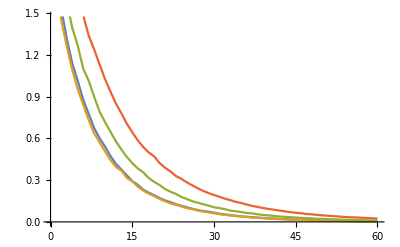

```mathematica
ListLinePlot[{t916sq/2.658,t9sq/2.63793*0.9,t8sq/2.35893*0.8,t7sq/2.00476*0.7}]
```

```mathematica
t916tri=Re[Flatten[Import["tgeneraldot916tri.dat"]]/(2π*re916)];
t9tri=0.9*Re[Flatten[Import["tgeneraldot9tri.dat"]]/(2π*re9)];
t8tri=0.8*Re[Flatten[Import["tgeneraldot8tri.dat"]]/(2π*re8)];
t7tri=0.8*Re[Flatten[Import["tgeneraldot7tri.dat"]]/(2π*re7)];
```

```mathematica
tcritri=Re[Flatten[Import["tcriticaltri.dat"]]*N[0.916/((0.158035^2)*2π)]];
```

```mathematica
tcrihc=Re[Flatten[Import["tcriticalhc.dat"]]*N[0.916/((0.158035^2)*2π)]];
```

```mathematica
tcrisq=Re[Flatten[Import["tsqrtcritical.dat"]]]*N[0.916/((0.158035^2)*2π)];
```

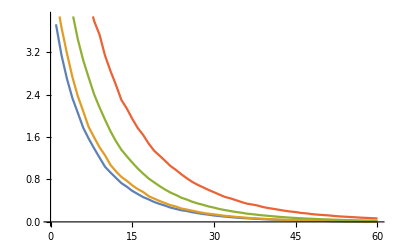

```mathematica
ListLinePlot[{tcritri/2.7063,t9tri/2.63793,t8tri/2.35893,t7tri/2.00476}]
```

```mathematica
]
```

```mathematica
t916hc=Re[Flatten[Import["tgeneraldot916hc.dat"]]/(2π*re916)];
t9hc=0.9*Re[Flatten[Import["tgeneraldot9hc.dat"]]/(2π*re9)];
t8hc=0.8*Re[Flatten[Import["tgeneraldot8hc.dat"]]/(2π*re8)];
t7hc=0.7*Re[Flatten[Import["tgeneraldot7hc.dat"]]/(2π*re7)];
```

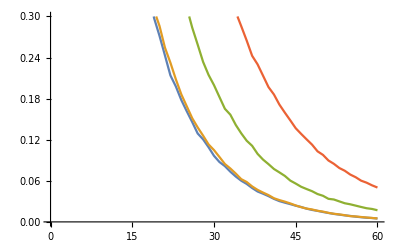

```mathematica
ListLinePlot[{t916hc/2.658,t9hc/2.63793,t8hc/2.35893,t7hc/2.00476},PlotRange->{0,0.3}]
```

```mathematica
J9=Re[Flatten[Import["Jgeneral9.dat"]]]*N[1/(2*re9^2*(2π)^2)];
```

```mathematica
J9n=Re[Flatten[Import["Jgeneral9normal.dat"]]]N[1/(2*re9^2*(2π)^2)];
```

```mathematica
J8=Re[Flatten[Import["Jgeneral8.dat"]]]N[1/(2*re8^2*(2π)^2)];
```

```mathematica
J7=Re[Flatten[Import["Jgeneral7.dat"]]]N[1/(2*re7^2*(2π)^2)];
0.0028347515196081273*N[1/(2*re7^2*(2π)^2)]
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

0.000456408+0. ⅈ

```mathematica
J916=Re[Flatten[Import["Jterm18.dat"]]]*N[1/((0.158659)^4*(2π)^2)]*0.5;
```

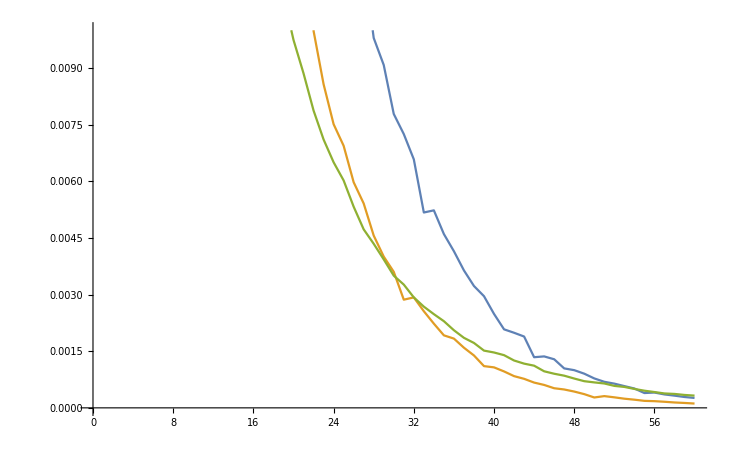

```mathematica
ListLinePlot[{J7,J8,J916},PlotRange->{0,0.01}]
```

```mathematica
t916hc^2/2.7
```

{22.4566,16.191,12.1537,9.15152,6.83895,5.18745,4.12364,3.097,2.42289,1.82047,1.37858,1.16059,0.908911,0.697914,0.554677,0.462457,0.360508,0.296101,0.231887,0.193141,0.154524,0.119749,0.102341,0.082897,0.0683411,0.0556535,0.0436579,0.0380237,0.0311058,0.024378,0.0200095,0.017344,0.0140627,0.01147,0.00946323,0.00804084,0.0064081,0.00515246,0.00443001,0.00370523,0.00295665,0.00240944,0.00206207,0.00175981,0.00146351,0.00123706,0.000974574,0.000798417,0.000678426,0.000546164,0.000445077,0.000354834,0.000294826,0.000237979,0.000199034,0.000152162,0.000122171,0.0000966251,0.0000842853,0.0000624278}

```mathematica
J9[[1]]
```

0.0260383

### Data files

```mathematica
tou501sqext=Flatten[Import["tgeneral501sqext.dat"]];t5=Table[Null,{i,89}];
```

```mathematica
For[i=1,i<90,i++,t5[[i]]={(i-1)*0.05+0.60,tou501sqext[[i]]^2*N[0.5/(2π*Re[re5])]^2/1.31602}]
Export["ttu5_sq.dat",t5]
```

ttu5_sq.dat

```mathematica
t6ext=Table[Null,{i,29}];t6=Table[Null,{i,60}];
```

```mathematica
For[i=1,i<61,i++,t6[[i]]={(i-1)*0.05+0.60,tgeneraldot6hc[[i]]*N[0.6/(2π*Re[re6])]/1.64636}]
```

```mathematica
Export["tou6_hc.dat",t6]
```

tou6_hc.dat

```mathematica
For[i=1,i<30,i++,t6ext[[i]]={(i-1)*0.05+3.60,tgeneral6sqext[[i]]^2*N[0.6/(Re[re6]*2π)]^2/1.64636}]
```

```mathematica
Export["ttu6sq_ext.dat",t6ext]
```

ttu6sq_ext.dat

```mathematica
tcriext=Table[Null,{i,29}];
```

```mathematica
For[i=1,i<30,i++,tcriext[[i]]={(i-1)*0.05+3.60,tgeneral916sqext[[i]]^2*N[0.916/(Re[re916]*2π)]^2/2.7063}]
```

```mathematica
Export["ttucri_sq_ext.dat",tcriext]
```

ttucri_sq_ext.dat

```mathematica
ttermext916=Table[Null,{i,29}];
```

```mathematica
For[i=1,i<30,i++,ttermext916[[i]]={(i-1)*0.05+3.60,tgeneral916hcext[[i]]*N[0.916/(Re[re916]*2π)]/2.7063}];
```

```mathematica
Export["toucrihc_ext.dat",ttermext916]
```

toucrihc_ext.dat

```mathematica
tgeneral916hcext
```

{1.23727×10^-8,1.2228×10^-8,1.07026×10^-8,9.51865×10^-9,8.09663×10^-9,7.46318×10^-9,6.5429×10^-9,5.29845×10^-9,4.6815×10^-9,4.45329×10^-9,3.57009×10^-9,3.32824×10^-9,2.69569×10^-9,2.37104×10^-9,1.69488×10^-9,1.25347×10^-9,7.68895×10^-10,7.89828×10^-10,4.52785×10^-10,1.06257×10^-10,-1.9272×10^-10,-4.16526×10^-10,-6.18593×10^-10,-6.56491×10^-10,-1.0519×10^-9,-1.28881×10^-9,-8.46499×10^-10,-1.28391×10^-9,-1.35255×10^-9}

```mathematica
For[i=1,i<30,i++,Jext6[[i]]={(i-1)*0.05+3.60,Jexgeneral6[[i]]}]
```

```mathematica
Export["J6ext.dat",Jext6]
```

J6ext.dat

```mathematica
J7ext=Flatten[Import["Jgeneral7ext.dat"]];
```

```mathematica
For[i=1,i<30,i++,J5[[i]]={(i-1)*0.05+3.60,J7ext[[i]]}]
Export["J7ext.dat",J7ext]
```

J7ext.dat

```mathematica
Jcriext=Flatten[Import["Jcriext8.dat"]];
Jcriex=Table[Null,{i,20}];
For[i=1,i<21,i++,Jcriex[[i]]={(i-1)*0.05+3.60,Jcriext[[i]]}]
Export["Jcriext.dat",Jcriex]
```

Jcriext.dat

```mathematica
Import["tou7hc.dat"]
```

```mathematica
tou7hc=Table[Null,{i,60}];
```

```mathematica
For[i=1,i<61,i++,tou7hc[[i]]={(i-1)*0.05+0.60,t7hc[[i]]/2.00476}]
```

```mathematica
Export["tou7hc.dat",tou7hc]
```

tou7hc.dat

```mathematica
Jterm7=Table[Null,{i,60}];
```

```mathematica
For[i=1,i<61,i++,Jterm7[[i]]={(i-1)*0.05+0.60,J7[[i]]}]
```

```mathematica
Export["J7.dat",Jterm7]
```

J7.dat

```mathematica
ttu9hc=Table[Null,{i,60}];
```

```mathematica
For[i=1,i<61,i++,ttu9hc[[i]]={(i-1)*0.05+0.60,t9hc[[i]]^2/2.63793}]
```

```mathematica
Export["ttu9_hc.dat",ttu9hc]
```

ttu9_hc.dat

### EXTENSION (From 3.60 to 5.00)

### J (g=0.8) extension

```mathematica
Jexgeneral8=Table[Null,{j,29}];
```

```mathematica
Re[Jgeneral[1/2,0.8,-0.48,3.6+0.05*(1-1)]]*Re[N[1/(2*re8^2*(2π)^2)]]
```

0.0000987031

```mathematica
ScientificForm[0.00009870310311602063]
```

9.87031×10^-5

```mathematica
NumberForm[0.00009870310311602063]
```

0.0000987031

```mathematica
Jexgeneral8
```

{0.000103225,0.0000941592,0.0000834413,0.000073869,0.0000681605,0.0000593602,0.0000532466,0.0000479416,0.0000445959,0.0000401694,0.0000366825,0.000031755,0.0000278863,0.0000251035,0.0000239146,0.0000210715,0.0000191912,0.000017305,0.0000149002,0.0000139567,0.0000123348,0.000010826,0.0000107117,8.81065×10^-6,8.85766×10^-6,8.11064×10^-6,6.96919×10^-6,6.17724×10^-6,5.27418×10^-6}

```mathematica
Jexgeneral8[[1]]
```

0.000103225

```mathematica
For[
i=1,
i<30,
i++,
Jexgeneral8[[i]]=Re[Jgeneral[1/2,0.8,-0.48,3.6+0.05*(i-1)]]*Re[N[1/(2*re8^2*(2π)^2)]]
];
Export["Jgeneral8ext.dat",Jexgeneral8]
```

```mathematica
Jexgeneral8[[29]]=Re[Jgeneral[1/2,0.8,-0.48,3.6+0.05*(29-1)]]*Re[N[1/(2*re8^2*(2π)^2)]]
```

5.27418×10^-6

```mathematica
Export["Jgeneral8ext.dat",Jexgeneral8]
```

Jgeneral8ext.dat

### J(g=0.9) extension

```mathematica
Jexgeneral9=Table[Null,{j,29}];
```

```mathematica
Jexgeneral9
```

{0.000205704,0.000209129,0.000189586,0.000174117,0.000158404,0.000151596,0.000137743,0.000115903,0.000141064,0.000109585,0.000103134,0.0000967594,0.0000911057,0.0000842643,0.0000794408,0.0000689239,0.0000659581,0.0000607199,0.0000591364,0.0000528708,0.0000499369,0.0000449639,0.0000442015,0.0000414005,0.000039359,0.0000364663,0.0000312944,0.000029875,0.0000285911}

```mathematica
For[
i=1,
i<30,
i++,
Jexgeneral9[[i]]=Re[Jgeneral[1/2,0.9,-0.92,3.6+0.05*(i-1)]]*Re[N[1/(2*re9^2*(2π)^2)]]
];
Export["Jgeneral9ext.dat",Jexgeneral9]
```

Jgeneral9ext.dat

### J(g=0.7) extension

```mathematica
Jexgeneral7=Table[Null,{j,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
Jexgeneral8[[i]]=Re[Jgeneral[1/2,0.8,-0.48,3.6+0.05*(i-1)]]*Re[N[1/(2*re8^2*(2π)^2)]]
];
Export["Jgeneral8ext.dat",Jexgeneral8]
```

### J(g=0.6)

```mathematica
Jexgeneral6=Table[Null,{j,29}];
```

```mathematica
For[
i=1,
i<30,
i++,
Jexgeneral6[[i]]=Re[Jgeneral[1/2,0.6,0.2198,3.6+0.05*(i-1)]]*Re[N[1/(2*re6^2*(2π)^2)]]
];
Export["Jgeneral6ext.dat",Jexgeneral6]
```

Jgeneral6ext.dat

```mathematica
J7mod=Flatten[Import["J7ext.dat"]]
```

{0.000232242,0.000212156,0.000178424,0.000168412,0.000153751,0.000133043,0.000118661,0.000104607,0.0000969735,0.0000863614,0.0000739365,0.0000697796,0.0000625708,0.0000547291,0.0000514525,0.0000448052,0.0000398138,0.0000313649,0.000029351,0.0000290163,0.0000245147,0.0000210779,0.0000199915,0.000016224,0.0000162936,0.000015036,0.0000129546,0.0000101121,0.0000102221}

```mathematica
For[i=1,i<30,i++,J7mod[[i]]={3.6+(i-1)*0.05,J7mod[[i]]}]
```

```mathematica
J7mod
```

{{3.6,0.000232242},{3.65,0.000212156},{3.7,0.000178424},{3.75,0.000168412},{3.8,0.000153751},{3.85,0.000133043},{3.9,0.000118661},{3.95,0.000104607},{4.,0.0000969735},{4.05,0.0000863614},{4.1,0.0000739365},{4.15,0.0000697796},{4.2,0.0000625708},{4.25,0.0000547291},{4.3,0.0000514525},{4.35,0.0000448052},{4.4,0.0000398138},{4.45,0.0000313649},{4.5,0.000029351},{4.55,0.0000290163},{4.6,0.0000245147},{4.65,0.0000210779},{4.7,0.0000199915},{4.75,0.000016224},{4.8,0.0000162936},{4.85,0.000015036},{4.9,0.0000129546},{4.95,0.0000101121},{5.,0.0000102221}}

```mathematica
Export["J7ext.dat",J7mod]
```

J7ext.dat

```mathematica
J7mod[[1,2]]
```

0.000232242

```mathematica
Directory[]
```

/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/ratio

```mathematica
SetDirectory["/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/ratio"]
```

/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/ratio

```mathematica
j5=Import["J5.dat"];
j6=Import["J6.dat"];
j7=Import["J7.dat"];
j8=Import["J8.dat"];
j9=Import["J9.dat"];
jcri=Import["Jcri.dat"];
```

```mathematica
ttucrisq=Import["ttucri_sq.dat"];
ttucritri=Import["ttucri_tri.dat"];
ttucrihc=Import["ttucri_hc.dat"];
```

```mathematica
ratiocrisq=Table[Null,{i,80}];
ratiocritri=Table[Null,{i,80}];
ratiocrihc=Table[Null,{i,80}];
```

```mathematica
For[i=1,i<81,i++,ratiocrisq[[i]]={(i-1)*0.05+0.60,Re[ttucrisq[[i,2]]]/Re[jcri[[i,2]]]}];
For[i=1,i<81,i++,ratiocritri[[i]]={(i-1)*0.05+0.60,Re[ttucritri[[i,2]]]/Re[jcri[[i,2]]]}];
For[i=1,i<81,i++,ratiocrihc[[i]]={(i-1)*0.05+0.60,Re[ttucrihc[[i,2]]]/Re[jcri[[i,2]]]}];
```

```mathematica
ratiocrihc
```

{{0.6,129.117},{0.65,113.806},{0.7,105.562},{0.75,88.9134},{0.8,78.8254},{0.85,66.1716},{0.9,61.4306},{0.95,58.3542},{1.,51.7023},{1.05,46.6257},{1.1,41.3824},{1.15,37.7534},{1.2,34.5721},{1.25,29.9619},{1.3,27.7187},{1.35,24.909},{1.4,21.066},{1.45,20.5688},{1.5,18.5377},{1.55,15.9845},{1.6,14.2758},{1.65,13.311},{1.7,12.0733},{1.75,10.6592},{1.8,9.4374},{1.85,8.94697},{1.9,8.23177},{1.95,7.35925},{2.,6.48484},{2.05,5.94346},{2.1,5.36981},{2.15,5.06865},{2.2,4.42635},{2.25,4.02928},{2.3,3.41825},{2.35,3.2462},{2.4,3.02232},{2.45,2.64553},{2.5,2.52991},{2.55,2.06812},{2.6,1.81823},{2.65,1.69106},{2.7,1.46742},{2.75,1.29857},{2.8,1.24904},{2.85,1.11963},{2.9,0.999045},{2.95,0.880559},{3.,0.779536},{3.05,0.646019},{3.1,0.572164},{3.15,0.550177},{3.2,0.44265},{3.25,0.416583},{3.3,0.365424},{3.35,0.306884},{3.4,0.28552},{3.45,0.237229},{3.5,0.184599},{3.55,0.170515},{3.6,1.49532},{3.65,1.55319},{3.7,1.35002},{3.75,1.12392},{3.8,0.858326},{3.85,0.83063},{3.9,0.623903},{3.95,0.444168},{4.,0.401429},{4.05,0.360017},{4.1,0.257959},{4.15,0.226766},{4.2,0.161397},{4.25,0.138243},{4.3,0.0724383},{4.35,0.0418448},{4.4,0.0171519},{4.45,0.0200874},{4.5,0.00682622},{4.55,0.00039051}}

```mathematica
Export["ratiocrisq.dat",ratiocrisq];Export["ratiocritri.dat",ratiocritri];Export["ratiocrihc.dat",ratiocrihc];
```

```mathematica
Directory[]
```

/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/ratio_data

```mathematica
SetDirectory["/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/CombinedJ"]
```

/Users/xudou/Google Drive/Notes/Superlattice_Impurity/datafiles/CombinedJ

```mathematica
Jd=Import["J7.dat"]
```

{{0.6,0.276173},{0.65,0.234934},{0.7,0.229151},{0.75,0.18893},{0.8,0.18061},{0.85,0.155408},{0.9,0.131273},{0.95,0.121277},{1.,0.107765},{1.05,0.0908043},{1.1,0.0784886},{1.15,0.0626092},{1.2,0.0627131},{1.25,0.0544592},{1.3,0.0510204},{1.35,0.0439579},{1.4,0.0425309},{1.45,0.0352619},{1.5,0.0305179},{1.55,0.0282918},{1.6,0.023513},{1.65,0.0215933},{1.7,0.0180289},{1.75,0.0164829},{1.8,0.0148325},{1.85,0.0131853},{1.9,0.0117911},{1.95,0.00979575},{2.,0.00907952},{2.05,0.00778296},{2.1,0.00725051},{2.15,0.00658164},{2.2,0.00517365},{2.25,0.0052304},{2.3,0.00460236},{2.35,0.00414785},{2.4,0.0036397},{2.45,0.00322695},{2.5,0.00295697},{2.55,0.00248766},{2.6,0.00207951},{2.65,0.00198862},{2.7,0.00188904},{2.75,0.00134129},{2.8,0.00136266},{2.85,0.00128682},{2.9,0.0010447},{2.95,0.000998251},{3.,0.000905197},{3.05,0.000779564},{3.1,0.000690022},{3.15,0.000641555},{3.2,0.000576123},{3.25,0.000512578},{3.3,0.000392442},{3.35,0.000405363},{3.4,0.000355668},{3.45,0.000323605},{3.5,0.000287727},{3.55,0.000262632},{3.6,0.000232242},{3.65,0.000212156},{3.7,0.000178424},{3.75,0.000168412},{3.8,0.000153751},{3.85,0.000133043},{3.9,0.000118661},{3.95,0.000104607},{4.,0.0000969735},{4.05,0.0000863614},{4.1,0.0000739365},{4.15,0.0000697796},{4.2,0.0000625708},{4.25,0.0000547291},{4.3,0.0000514525},{4.35,0.0000448052},{4.4,0.0000398138},{4.45,0.0000313649},{4.5,0.000029351},{4.55,0.0000290163},{4.6,0.0000245147},{4.65,0.0000210779},{4.7,0.0000199915},{4.75,0.000016224},{4.8,0.0000162936},{4.85,0.000015036},{4.9,0.0000129546},{4.95,0.0000101121},{5.,0.0000102221}}

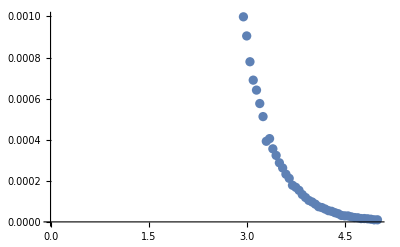

```mathematica
ListPlot[Jd,PlotRange->{0,0.001}]
```

```mathematica
N[0.010856495637647508/0.000456408]
```

23.7868

### Modification 0.7 triangular

```mathematica
tgeneral7triext=Import["tamend7triext.dat"];
```

```mathematica
For[
i=1,
i<30,
i++,
tgeneral7triext[[i]]={3.6+0.05*(i-1),Re[tgeneraltri[1/2,0.7,-0.098,3.6+0.05*(i-1)]]*N[1/(2*re7^2*(2π)^2)]}
];
Export["tamend7triext.dat",tgeneral7triext]
```

tamend7triext.dat

```mathematica
tgeneral7triext[[1,2]]
```

0.0338918+0. ⅈ

```mathematica
For[
i=1,
i<30,
i++,
tgeneral7triext[[i]]={3.6+0.05*(i-1),Re[0.7/(2π*re7)*tgeneral7triext[[i,2]]]/Re[N[1/(2*re7^2*(2π)^2)]]}
];
```

```mathematica
Export["t7triamendext.dat",tgeneral7triext]
```

t7triamendext.dat

```mathematica
tgeneraltri[1/2,0.7,-0.098,3.6]*0.7/(2π*re7)/2.00476
```

0.0423804-0.000422504 ⅈ

```mathematica
t7tri=Table[Null,{i,60}];
For[
i=1,
i<61,
i++,
t7tri[[i]]={0.6+0.05*(i-1),Re[tgeneraltri[1/2,0.7,-0.098,0.6+0.05*(i-1)]]*Re[0.7/(2π*re7)]}
];
```

```mathematica
Export["t7tri.dat",t7tri]
```

t7tri.dat

```mathematica
tdata=Import["t7tri.dat"]
ttu7triamend=Table[Null,{i,89}];
```

{{0.6,11.5238},{0.65,10.2602},{0.7,9.20522},{0.75,8.25372},{0.8,7.4871},{0.85,6.64093},{0.9,5.99978},{0.95,5.43435},{1.,4.88559},{1.05,4.40425},{1.1,3.92561},{1.15,3.62291},{1.2,3.29326},{1.25,2.99531},{1.3,2.7502},{1.35,2.50474},{1.4,2.26387},{1.45,2.09091},{1.5,1.923},{1.55,1.76402},{1.6,1.61944},{1.65,1.4579},{1.7,1.34034},{1.75,1.25122},{1.8,1.15077},{1.85,1.06472},{1.9,0.977939},{1.95,0.905603},{2.,0.841448},{2.05,0.792319},{2.1,0.710096},{2.15,0.662936},{2.2,0.623929},{2.25,0.57384},{2.3,0.539493},{2.35,0.496613},{2.4,0.459912},{2.45,0.428171},{2.5,0.391654},{2.55,0.368546},{2.6,0.340546},{2.65,0.317458},{2.7,0.302094},{2.75,0.27743},{2.8,0.256376},{2.85,0.243285},{2.9,0.220883},{2.95,0.205615},{3.,0.193705},{3.05,0.183329},{3.1,0.166704},{3.15,0.158215},{3.2,0.145969},{3.25,0.137927},{3.3,0.126254},{3.35,0.121185},{3.4,0.112115},{3.45,0.101155},{3.5,0.0986509},{3.55,0.0923135},{3.6,0.0836157},{3.65,0.0802965},{3.7,0.0755214},{3.75,0.0697882},{3.8,0.0656886},{3.85,0.0611268},{3.9,0.058176},{3.95,0.0533763},{4.,0.0503136},{4.05,0.0473077},{4.1,0.0441692},{4.15,0.0411299},{4.2,0.0394512},{4.25,0.0370682},{4.3,0.034562},{4.35,0.0318518},{4.4,0.0302407},{4.45,0.0286563},{4.5,0.0267099},{4.55,0.0253125},{4.6,0.0236178},{4.65,0.0223132},{4.7,0.0206294},{4.75,0.0195279},{4.8,0.0180557},{4.85,0.017257},{4.9,0.0162814},{4.95,0.0150271},{5.,0.0143396}}

```mathematica
For[
i=1,
i<90,
i++,
ttu7triamend[[i]]={0.6+0.05*(i-1),tdata[[i,2]]^2/2.00476}];
```

```mathematica
ttu7triamend
```

{{0.6,66.2409},{0.65,52.5111},{0.7,42.2675},{0.75,33.9811},{0.8,27.9618},{0.85,21.9986},{0.9,17.956},{0.95,14.731},{1.,11.9061},{1.05,9.6757},{1.1,7.68693},{1.15,6.54715},{1.2,5.40991},{1.25,4.4753},{1.3,3.77281},{1.35,3.12941},{1.4,2.55646},{1.45,2.18077},{1.5,1.84457},{1.55,1.55219},{1.6,1.30818},{1.65,1.06022},{1.7,0.896127},{1.75,0.780921},{1.8,0.660562},{1.85,0.565467},{1.9,0.477047},{1.95,0.409085},{2.,0.353177},{2.05,0.313139},{2.1,0.25152},{2.15,0.219221},{2.2,0.194181},{2.25,0.164255},{2.3,0.145181},{2.35,0.12302},{2.4,0.105509},{2.45,0.0914476},{2.5,0.0765144},{2.55,0.0677518},{2.6,0.0578482},{2.65,0.0502701},{2.7,0.0455222},{2.75,0.0383924},{2.8,0.0327862},{2.85,0.0295236},{2.9,0.0243367},{2.95,0.0210886},{3.,0.0187164},{3.05,0.0167648},{3.1,0.0138621},{3.15,0.0124863},{3.2,0.0106282},{3.25,0.00948931},{3.3,0.00795105},{3.35,0.00732543},{3.4,0.00626997},{3.45,0.00510407},{3.5,0.00485445},{3.55,0.00425077},{3.6,0.00348749},{3.65,0.00321611},{3.7,0.00284497},{3.75,0.00242942},{3.8,0.00215237},{3.85,0.00186381},{3.9,0.0016882},{3.95,0.00142113},{4.,0.00126272},{4.05,0.00111635},{4.1,0.000973143},{4.15,0.000843824},{4.2,0.000776351},{4.25,0.000685396},{4.3,0.000595846},{4.35,0.000506065},{4.4,0.000456163},{4.45,0.000409616},{4.5,0.000355862},{4.55,0.0003196},{4.6,0.000278238},{4.65,0.000248348},{4.7,0.000212281},{4.75,0.000190217},{4.8,0.000162617},{4.85,0.000148548},{4.9,0.000132227},{4.95,0.000112639},{5.,0.000102568}}

```mathematica
jdata=Import["J7.dat"];Ratio7trinew=Table[Null,{i,89}];
```

```mathematica
For[
i=1,
i<90,
i++,
Ratio7trinew[[i]]={0.6+0.05*(i-1),ttu7triamend[[i,2]]/jdata[[i,2]]}];
Export["Ratio7tri_new.dat",Ratio7trinew]
```

Ratio7tri_new.dat

```mathematica
Export["tou7mend.dat",tou7mend]
```

tou7mend.dat

```mathematica
tou7mend=Table[Null,{i,60}];
For[
i=1,
i<61,
i++,
tou7mend[[i]]={0.6+0.05*(i-1),t7tri[[i,2]]/2.00476}
];
```

```mathematica
toutri7mend=Table[Null,{i,29}];
For[
i=1,
i<30,
i++,
toutri7mend[[i]]={3.6+0.05*(i-1),Re[tgeneral7triext[[i,2]]]/2.00476}
];
```

```mathematica
Export["toumend7tri.dat",toutri7mend]
```

toumend7tri.dat

```mathematica
Dist2[a_,x_,θ_]:=√(3*a^2+x^2+√3*a*x*Sin[θ]-3*a*x*Cos[θ])
```

```mathematica
tnexttri[j_,g_,ϵ_,sd_]:=NIntegrate[x*(OutsF[j,g,ϵ,Dist2[sd,x,θ]]*Conjugate[OutsF[j,g,ϵ,x]]+OutsG[j,g,ϵ,Dist2[sd,x,θ]]*Conjugate[OutsG[j,g,ϵ,x]]*nphase1[sd,x,θ])*(1/(√(x^2+sd^2-2*x*sd*Cos[θ]))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]+sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]-3*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-3*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ])^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-3*sd)^2+(x*Sin[θ])^2))+1/(√((x*Cos[θ]+3*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]+3*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]-5*sd/2)^2+(x*Sin[θ]-√3*sd/2)^2))+1/(√((x*Cos[θ]-5*sd/2)^2+(x*Sin[θ]+√3*sd/2)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]+sd)^2+(x*Sin[θ]+√3*sd)^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ]-√3*sd)^2))+1/(√((x*Cos[θ]-2*sd)^2+(x*Sin[θ]+√3*sd)^2))),{x,1/18,20},{θ,0,2π}];
```

```mathematica
nCosRplusr[R_,r_,ϕ_]:=(r*Cos[ϕ]-3*R/2)/(√(3*R^2+r^2+√3*R*r*Sin[ϕ]-3*R*r*Cos[ϕ]));(*compute augular difference between r-R' and R*)
nSinRplusr[R_,r_,ϕ_]:=(r*Sin[ϕ]+(√3)/2*R)/(√(3*R^2+r^2+√3*R*r*Sin[ϕ]-3*R*r*Cos[ϕ]));
nphase1[R_,r_,ϕ_]:=(nCosRplusr[R,r,ϕ]Cos[ϕ]+nSinRplusr[R,r,ϕ]Sin[ϕ])+I*(nSinRplusr[R,r,ϕ]Cos[ϕ]-nCosRplusr[R,r,ϕ]Sin[ϕ]);(*Compute phases due to the angular difference*)
nphase2[R_,r_,ϕ_]:=(nCosRplusr[R,r,ϕ]Cos[ϕ]+nSinRplusr[R,r,ϕ]Sin[ϕ])-I*(nSinRplusr[R,r,ϕ]Cos[ϕ]-nCosRplusr[R,r,ϕ]Sin[ϕ]);
```

```mathematica
N[nSinRplusr[1,1,1]]
```

0.871743

```mathematica
(Re[Re[0.916/(2π*re916)]*tnexttri[1/2,0.916,-0.99,3.8]]/Re[(Re[0.916/(2π*re916)]*tgeneraltri[1/2,0.916,-0.99,3.8])])^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {6.58185, 5.75959}. NIntegrate obtained -9.40875×10^-9 + 5.94882×10^-10\ ⅈ and 1.7079×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x, θ} = {3.8, 6.2831773838340207592151440314787169683086176519282162189483642578}. NIntegrate obtained 1.28092×10^-8 - 1.35667×10^-10\ ⅈ and 1.75533×10^-10 for the integral and error estimates.

0.539534

```mathematica
a=Table[Null,{i,16}];
```

```mathematica
For[
i=1,
i<17,
i++,
a[[i]]={1.5+(i-1)*0.1,(Re[Re[0.916/(2π*re916)]*tnexttri[1/2,0.916,-0.99,1.5+(i-1)*0.1]]/Re[(Re[0.916/(2π*re916)]*tgeneraltri[1/2,0.916,-0.99,1.5+(i-1)*0.1])])^2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {2.59813, 5.75959}. NIntegrate obtained 2.34199×10^-7 + 4.49887×10^-8\ ⅈ and 4.66959×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x, θ} = {1.50004, 0.000120264}. NIntegrate obtained 1.59373×10^-6 - 1.25607×10^-20\ ⅈ and 2.53836×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {2.77129, 5.75959}. NIntegrate obtained 1.61694×10^-7 + 3.57092×10^-8\ ⅈ and 5.07711×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
a
```

{{1.5,0.0215943},{1.6,0.0157688},{1.7,0.0108358},{1.8,0.00711335},{1.9,0.00375599},{2.,0.00195861},{2.1,0.000600786},{2.2,0.000174489},{2.3,0.000181847},{2.4,0.00122106},{2.5,0.00285097},{2.6,0.00834487},{2.7,0.0102824},{2.8,0.0155564},{2.9,0.0256972},{3.,0.0322731}}

```mathematica
Export["superexchangeratio.dat",a]
```

superexchangeratio.dat

```mathematica
b=Table[Null,{i,16}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
For[
i=1,
i<17,
i++,
b[[i]]={3.1+(i-1)*0.1,(Re[Re[0.916/(2π*re916)]*tnexttri[1/2,0.916,-0.99,3.1+(i-1)*0.1]]/Re[(Re[0.916/(2π*re916)]*tgeneraltri[1/2,0.916,-0.99,3.1+(i-1)*0.1])])^2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {5.3694, 5.75959}. NIntegrate obtained -1.40188×10^-8 + 2.73436×10^-9\ ⅈ and 6.24844×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x, θ} = {3.10004, 6.2831773838340207592151440314787169683086176519282162189483642578}. NIntegrate obtained 6.68575×10^-8 - 2.71381×10^-11\ ⅈ and 6.98125×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {5.54301, 5.75959}. NIntegrate obtained -1.34829×10^-8 + 2.05116×10^-9\ ⅈ and 2.45959×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
b
```

{{3.1,0.0439666},{3.2,0.0613449},{3.3,0.0855377},{3.4,0.119135},{3.5,0.162001},{3.6,0.229553},{3.7,0.326247},{3.8,0.539645},{3.9,0.818343},{4.,1.43146},{4.1,3.2447},{4.2,10.8914},{4.3,271.8},{4.4,29.2056},{4.5,5.20981},{4.6,2.52624}}

```mathematica
Re[0.916/(2π*re916)]*tnexttri[1/2,0.916,-0.99,4.3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ near {x, θ} = {7.44794, 5.75959}. NIntegrate obtained -6.03013×10^-9 + 4.52249×10^-10\ ⅈ and 5.11855×10^-10 for the integral and error estimates.

-0.00385324+0.000288986 ⅈ